# Homework 6

ODE for problem 1

```mathematica
DSolve[{y'[t]==-(3t/(1+t))y[t]+2(1+t)^3 ⅇ^-t,y[0]==1},y[t],t]
```

{{y[t]→ⅇ^-t (1+t)^3}}

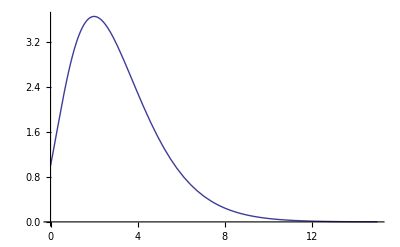

```mathematica
Plot[ⅇ^-t (1+t)^3, {t, 0, 15}]
```

```mathematica
Factor[yn  (1+8/15 h α)+5/12 h α yn  (1+8/15 h α)-17/60 h α yn]
```

1/9 yn (9+6 h α+2 h^2 α^2)

```mathematica
k1=yn  (1+8/15 h α)
k2=1/9 yn (9+6 h α+2 h^2 α^2)
k3=(1+3/4 h α)k2 -5/12 α h k1
```

yn (1+(8 h α)/15)

1/9 yn (9+6 h α+2 h^2 α^2)

-5/12 h yn α (1+(8 h α)/15)+1/9 yn (1+(3 h α)/4) (9+6 h α+2 h^2 α^2)

```mathematica
Factor [%]
```

1/6 yn (6+6 h α+3 h^2 α^2+h^3 α^3)